```mathematica
LoadPauliMatrices[]
```

Matrices loaded: σ0 (=1), σx, σy, σz, σp, σm, GMAT[θ,ϕ]

Create a product state of two qubits

```mathematica
Clear[β]
```

```mathematica
ρA = MatrixExp[-β σz/2];
ρA = ρA/Tr[ρA]//Simplify//mf;

ψB = 1/(√2){1,1};
ρB = out[ψB,ψB]//mf;
```

(1/(1+ⅇ^β) | 0
0 | ⅇ^β/(1+ⅇ^β))

(1/2 | 1/2
1/2 | 1/2)

```mathematica
vonNeumann[ρA]
```

-Log[1/(1+ⅇ^β)]/(1+ⅇ^β)-(ⅇ^β Log[ⅇ^β/(1+ⅇ^β)])/(1+ⅇ^β)

```mathematica
vonNeumann[ρB]
```

0

```mathematica
RelativeEntropy[ρA,ρB]
```

(1/(1+ⅇ^β)+ⅇ^β/(1+ⅇ^β)) ∞+Log[1/(1+ⅇ^β)]/(1+ⅇ^β)+(ⅇ^β Log[ⅇ^β/(1+ⅇ^β)])/(1+ⅇ^β)

```mathematica
RelativeEntropy[ρB,ρA]
```

-1/2 Log[1/(1+ⅇ^β)]-1/2 Log[ⅇ^β/(1+ⅇ^β)]

```mathematica
ρAB = kron[ρA,ρB]//mf;
```

(1/(2 (1+ⅇ^β)) | 1/(2 (1+ⅇ^β)) | 0 | 0
1/(2 (1+ⅇ^β)) | 1/(2 (1+ⅇ^β)) | 0 | 0
0 | 0 | ⅇ^β/(2 (1+ⅇ^β)) | ⅇ^β/(2 (1+ⅇ^β))
0 | 0 | ⅇ^β/(2 (1+ⅇ^β)) | ⅇ^β/(2 (1+ⅇ^β)))

Create a 2-qubit interaction

```mathematica
LoadSpinChainMatrices[2,"a"]
```

Matrices loaded: σ0 (=1), σx, σy, σz, σp, σm, eye, sm, sp, sx, sy, sz, c, cd

```mathematica
H = sx[1].sx[2]+sy[1].sy[2]+sz[1].sz[2];
U = MatrixExp[-ⅈ H t]//cf//mf;
```

(ⅇ^(-ⅈ t) | 0 | 0 | 0
0 | ⅇ^(ⅈ t) Cos[2 t] | (-ⅈ Cos[t]+Sin[t]) Sin[2 t] | 0
0 | (-ⅈ Cos[t]+Sin[t]) Sin[2 t] | ⅇ^(ⅈ t) Cos[2 t] | 0
0 | 0 | 0 | ⅇ^(-ⅈ t))

Entangle the two qubits

```mathematica
ρABp = U.ρAB.U†//cf//mf;
```

(1/(2+2 ⅇ^β) | (1+ⅇ^(-4 ⅈ t))/(4+4 ⅇ^β) | (1-ⅇ^(-4 ⅈ t))/(4+4 ⅇ^β) | 0
(1+ⅇ^(4 ⅈ t))/(4+4 ⅇ^β) | 1/4 (1-Cos[4 t] Tanh[β/2]) | -1/4 ⅈ Sin[4 t] Tanh[β/2] | -(ⅇ^β (-1+ⅇ^(4 ⅈ t)))/(4 (1+ⅇ^β))
(1-ⅇ^(4 ⅈ t))/(4+4 ⅇ^β) | 1/4 ⅈ Sin[4 t] Tanh[β/2] | 1/4 (1+Cos[4 t] Tanh[β/2]) | (ⅇ^β+ⅇ^(4 ⅈ t+β))/(4+4 ⅇ^β)
0 | (ⅈ ⅇ^(-2 ⅈ t+β) Cos[t] Sin[t])/(1+ⅇ^β) | (ⅇ^(-2 ⅈ t+β) Cos[2 t])/(2+2 ⅇ^β) | 1/(2+2 ⅇ^-β))

Calculate the reduced density matrix

```mathematica
ρAp = PTr[ρABp,{2}]//cf//mf;
ρBp = PTr[ρABp,{1}]//cf//mf;
```

(1/4+1/(2+2 ⅇ^β)-1/4 Cos[4 t] Tanh[β/2] | Csch[β] Sin[2 t] Sin[2 t-(ⅈ β)/2] Sinh[β/2]
Csch[β] Sin[2 t] Sin[2 t+(ⅈ β)/2] Sinh[β/2] | (1+3 ⅇ^β+(-1+ⅇ^β) Cos[4 t])/(4 (1+ⅇ^β)))

(1/4+1/(2+2 ⅇ^β)+1/4 Cos[4 t] Tanh[β/2] | 1/4 (1+Cos[4 t]+ⅈ Sin[4 t] Tanh[β/2])
1/4 (1+Cos[4 t+(ⅈ β)/2] Sech[β/2]) | (1-ⅇ^β (-3+Cos[4 t])+Cos[4 t])/(4 (1+ⅇ^β)))

Calculate expectation values of observables

```mathematica
Tr[sx[1].ρABp]//cf
Tr[σx.ρAp]//cf
```

Sin[2 t]^2

Sin[2 t]^2

Study the purity of the various states

```mathematica
Tr[ρAB.ρAB]//cf
Tr[ρABp.ρABp]//cf
(* Purity is invariant under unitary transformations *)
```

1/(1+Sech[β])

1/(1+Sech[β])

```mathematica
Tr[ρA.ρA]//cf
(* All the mixedness comes from A, because B is in a pure state *)
```

1/(1+Sech[β])

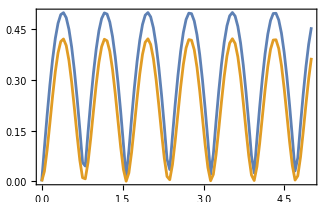

```mathematica
ListLinePlot[
{Table[{t,Concurrence[ρABp/.{β->1}]},{t,linspace[0,5,100]}],
Table[{t,MutualInformation[ρABp/.{β->1},{1,2}]},{t,linspace[0,5,100]}]
}]
```

Dephasing noise acting only on qubit 1, acting on the final state

```mathematica
ρABpp = Λ ρABp + (1-Λ)sz[1].ρABp.sz[1]//cf//mf;
```

(1/(2+2 ⅇ^β) | (1+ⅇ^(-4 ⅈ t))/(4+4 ⅇ^β) | -((-1+ⅇ^(-4 ⅈ t)) (-1+2 Λ))/(4 (1+ⅇ^β)) | 0
(1+ⅇ^(4 ⅈ t))/(4+4 ⅇ^β) | 1/4 (1-Cos[4 t] Tanh[β/2]) | -1/4 ⅈ (-1+2 Λ) Sin[4 t] Tanh[β/2] | -(ⅇ^β (-1+ⅇ^(4 ⅈ t)) (-1+2 Λ))/(4 (1+ⅇ^β))
-((-1+ⅇ^(4 ⅈ t)) (-1+2 Λ))/(4 (1+ⅇ^β)) | 1/4 ⅈ (-1+2 Λ) Sin[4 t] Tanh[β/2] | 1/4 (1+Cos[4 t] Tanh[β/2]) | (ⅇ^β+ⅇ^(4 ⅈ t+β))/(4+4 ⅇ^β)
0 | (ⅈ ⅇ^(-2 ⅈ t+β) (-1+2 Λ) Cos[t] Sin[t])/(1+ⅇ^β) | (ⅇ^(-2 ⅈ t+β) Cos[2 t])/(2+2 ⅇ^β) | 1/(2+2 ⅇ^-β))

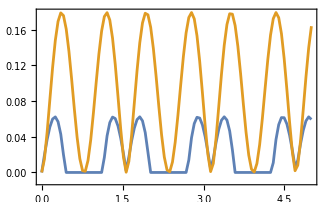

```mathematica
ListLinePlot[
{Table[{t,Concurrence[ρABpp/.{β->1,Λ->0.3}]},{t,linspace[0,5,100]}],
Table[{t,MutualInformation[ρABpp/.{β->1,Λ->0.3},{1,2}]},{t,linspace[0,5,100]}]},PlotRange->{-0.01,All}]
```

### Redfield & Numerics

```mathematica
LoadSpinChainMatrices[2];
H = sx[1].sx[2]+sy[1].sy[2]+sz[1].sz[2];
```

```mathematica
{energies,S} = Eigensystem[H]
```

{{-3.,1.,1.,1.},{{0.+0. ⅈ,0.707107+0. ⅈ,-0.707107+0. ⅈ,0.+0. ⅈ},{1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.707107+0. ⅈ,0.707107+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ}}}

```mathematica
c = sx[1];
T = 0.5;
γ = 1.0;
J[ω_]:=γ/(γ^2+ω^2);
dissipator = RedfieldDissipatorBosonicBath[energies,S,c,T,J];
liouv = UnitaryToVec[H]+dissipator;
```

```mathematica
ρ0 = Proj[4,4,4]//mf;
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
ρt = mesolve[liouv,ρ0,tf=10];
```

Plot the population of site 2 as a function of time

```mathematica
tab = Chop@Table[{t,Tr[sp[2].sm[2].ρt[t]]},{t,0,tf,0.1}];
```

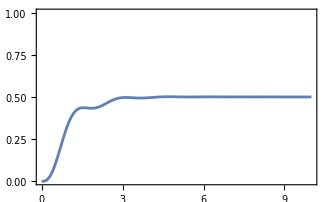

```mathematica
ListLinePlot[tab,PlotRange->{0,1}]
```

System subject to two baths, the 2nd one now coupled to site L

### Numerics more seriously

```mathematica
Clear[J,H,c1,c2,γ];
LoadSpinChainMatrices[L=4];
H =Sum[sz[i],{i,1,L}]+ Sum[sx[i].sx[i+1]+sy[i].sy[i+1](*+sz[i].sz[i+1]*),{i,1,L-1}];
{energies,S} = Eigensystem[H];

c1 = sx[1];
c2 = sx[L];
T1 = 1.5;
T2 = 3.0;
γ = 1.0;
J[ω_]:=γ ω;
dissipator1 = RedfieldDissipatorBosonicBath[energies,S,c1,T1,J];
dissipator2 = RedfieldDissipatorBosonicBath[energies,S,c2,T2,J];

(*dissipator1 = GlobalMasterEquationDissipator[energies,S,c1,T1,J];
dissipator2 = GlobalMasterEquationDissipator[energies,S,c2,T2,J];
*)
liouv = UnitaryToVec[H]+dissipator1+dissipator2//SparseArray;

ρ0 = kron@@Table[σm.σp,{L}];
U = CNOT[1,L,L].Hadamard[1,L];
ρ0 = U.ρ0.U†;
(*ρ0 = kron@@Table[0.3 σm.σp + 0.7 σp.σm,{L}];*)
Quiet@ReverseSort@Chop@Eigenvalues[L];
```

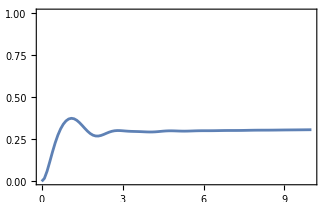

```mathematica
ρt = mesolve[liouv,ρ0,tf=10,True];tab = Chop@Table[{t,Tr[sp[2].sm[2].ρt[t]]},{t,0,tf,0.1}];
ListLinePlot[tab,PlotRange->{0,1}]
```

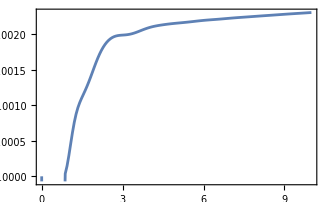

```mathematica
ListLinePlot@Table[{t,Chop@Min@Chop@Eigenvalues@ρt[t]},{t,linspace[0,tf,150]}]
```

```mathematica
ρt[tf]//mf;
```

(0.00293029 | 0 | 0 | -0.00094691+0.00048516 ⅈ | 0 | 0.000559906+0.000534783 ⅈ | 0.00124553+0.000680951 ⅈ | 0 | 0 | 0.000285709-0.000126695 ⅈ | 0.00102148-0.00024803 ⅈ | 0 | 0.00119524-0.000891502 ⅈ | 0 | 0 | -0.000328196+0.000359492 ⅈ
0 | 0.00918 | -0.00832705-0.00122906 ⅈ | 0 | 0.00396977+0.00236825 ⅈ | 0 | 0 | 0.00359385+0.00377981 ⅈ | -0.000579564-0.00199824 ⅈ | 0 | 0 | 0.00458326-0.000467457 ⅈ | 0 | 0.00350894-0.00333975 ⅈ | -0.00513675+0.000558497 ⅈ | 0
0 | -0.00832705+0.00122906 ⅈ | 0.0159687 | 0 | -0.0103815-0.0024221 ⅈ | 0 | 0 | -0.00312051-0.00526312 ⅈ | 0.00606709+0.00290487 ⅈ | 0 | 0 | -0.00679721+0.00188952 ⅈ | 0 | -0.00127655+0.00448433 ⅈ | 0.0122412-0.00224805 ⅈ | 0
-0.00094691-0.00048516 ⅈ | 0 | 0 | 0.0262343 | 0 | -0.0203412-0.00278863 ⅈ | 0.00656227-0.00209481 ⅈ | 0 | 0 | 0.0164086+0.00365866 ⅈ | -0.0132354+9.01902×10^-7 ⅈ | 0 | 0.00493616+0.00137047 ⅈ | 0 | 0 | 0.0252427-0.000999327 ⅈ
0 | 0.00396977-0.00236825 ⅈ | -0.0103815+0.0024221 ⅈ | 0 | 0.0181135 | 0 | 0 | -0.00118993+0.00434673 ⅈ | -0.012377-0.00142014 ⅈ | 0 | 0 | 0.00632558-0.00343691 ⅈ | 0 | -0.00297315-0.00392076 ⅈ | -0.0147428+0.00219974 ⅈ | 0
0.000559906-0.000534783 ⅈ | 0 | 0 | -0.0203412+0.00278863 ⅈ | 0 | 0.0496587 | -0.0350896-0.00258567 ⅈ | 0 | 0 | -0.0363431-0.00228667 ⅈ | 0.0310213+0.00239282 ⅈ | 0 | -0.0119716+0.0000366296 ⅈ | 0 | 0 | -0.0448398-0.00486434 ⅈ
0.00124553-0.000680951 ⅈ | 0 | 0 | 0.00656227+0.00209481 ⅈ | 0 | -0.0350896+0.00258567 ⅈ | 0.0606161 | 0 | 0 | 0.0252926-0.000307888 ⅈ | -0.0431766-0.00280535 ⅈ | 0 | 0.00547293-0.00335128 ⅈ | 0 | 0 | 0.0386399+0.00828829 ⅈ
0 | 0.00359385-0.00377981 ⅈ | -0.00312051+0.00526312 ⅈ | 0 | -0.00118993-0.00434673 ⅈ | 0 | 0 | 0.0989566 | 0.00136433+0.00234568 ⅈ | 0 | 0 | -0.0647884-0.00548245 ⅈ | 0 | -0.00892761-0.0064367 ⅈ | 0.0304781+0.00898163 ⅈ | 0
0 | -0.000579564+0.00199824 ⅈ | 0.00606709-0.00290487 ⅈ | 0 | -0.012377+0.00142014 ⅈ | 0 | 0 | 0.00136433-0.00234568 ⅈ | 0.0145015 | 0 | 0 | -0.00518495+0.00369215 ⅈ | 0 | 0.0042878+0.00296434 ⅈ | 0.0119492-0.00120348 ⅈ | 0
0.000285709+0.000126695 ⅈ | 0 | 0 | 0.0164086-0.00365866 ⅈ | 0 | -0.0363431+0.00228667 ⅈ | 0.0252926+0.000307888 ⅈ | 0 | 0 | 0.0439863 | -0.037918-0.00249968 ⅈ | 0 | 0.0163844+0.0035255 ⅈ | 0 | 0 | 0.0401894+0.00775074 ⅈ
0.00102148+0.00024803 ⅈ | 0 | 0 | -0.0132354-9.01902×10^-7 ⅈ | 0 | 0.0310213-0.00239282 ⅈ | -0.0431766+0.00280535 ⅈ | 0 | 0 | -0.037918+0.00249968 ⅈ | 0.0639619 | 0 | -0.02385-0.00286688 ⅈ | 0 | 0 | -0.0406917-0.0129156 ⅈ
0 | 0.00458326+0.000467457 ⅈ | -0.00679721-0.00188952 ⅈ | 0 | 0.00632558+0.00343691 ⅈ | 0 | 0 | -0.0647884+0.00548245 ⅈ | -0.00518495-0.00369215 ⅈ | 0 | 0 | 0.0972273 | 0 | -0.0296717-0.00445339 ⅈ | -0.0149777-0.00655463 ⅈ | 0
0.00119524+0.000891502 ⅈ | 0 | 0 | 0.00493616-0.00137047 ⅈ | 0 | -0.0119716-0.0000366296 ⅈ | 0.00547293+0.00335128 ⅈ | 0 | 0 | 0.0163844-0.0035255 ⅈ | -0.02385+0.00286688 ⅈ | 0 | 0.037433 | 0 | 0 | 0.00746207+0.00929354 ⅈ
0 | 0.00350894+0.00333975 ⅈ | -0.00127655-0.00448433 ⅈ | 0 | -0.00297315+0.00392076 ⅈ | 0 | 0 | -0.00892761+0.0064367 ⅈ | 0.0042878-0.00296434 ⅈ | 0 | 0 | -0.0296717+0.00445339 ⅈ | 0 | 0.0960478 | -0.0669478-0.00669183 ⅈ | 0
0 | -0.00513675-0.000558497 ⅈ | 0.0122412+0.00224805 ⅈ | 0 | -0.0147428-0.00219974 ⅈ | 0 | 0 | 0.0304781-0.00898163 ⅈ | 0.0119492+0.00120348 ⅈ | 0 | 0 | -0.0149777+0.00655463 ⅈ | 0 | -0.0669478+0.00669183 ⅈ | 0.135261 | 0
-0.000328196-0.000359492 ⅈ | 0 | 0 | 0.0252427+0.000999327 ⅈ | 0 | -0.0448398+0.00486434 ⅈ | 0.0386399-0.00828829 ⅈ | 0 | 0 | 0.0401894-0.00775074 ⅈ | -0.0406917+0.0129156 ⅈ | 0 | 0.00746207-0.00929354 ⅈ | 0 | 0 | 0.229924)

```mathematica
ρss=SteadyState[L]//mf;
```

(0.00335132 | 0 | 0 | -0.00122579+0.000304656 ⅈ | 0 | 0.000370697+0.000331061 ⅈ | 0.000178271+0.000264919 ⅈ | 0 | 0 | 0.0000536134-0.000310483 ⅈ | -0.00030804-0.000179887 ⅈ | 0 | 0.000952133-0.000569575 ⅈ | 0 | 0 | -0.00025278+0.000332935 ⅈ
0 | 0.0106229 | -0.00941256-0.00160002 ⅈ | 0 | 0.00416334+0.00277337 ⅈ | 0 | 0 | -0.000326752+0.00131061 ⅈ | -0.000936123-0.00195966 ⅈ | 0 | 0 | -0.00015706-0.000784957 ⅈ | 0 | 0.00278454-0.00177332 ⅈ | -0.00260718+0.00144529 ⅈ | 0
0 | -0.00941256+0.00160002 ⅈ | 0.0179973 | 0 | -0.0131887-0.00308187 ⅈ | 0 | 0 | 0.00248624-0.00250852 ⅈ | 0.00553459+0.00354551 ⅈ | 0 | 0 | -0.00168353+0.00123184 ⅈ | 0 | -0.00164378+0.00182064 ⅈ | 0.00408046-0.00342383 ⅈ | 0
-0.00122579-0.000304656 ⅈ | 0 | 0 | 0.0303233 | 0 | -0.0288936-0.004122 ⅈ | 0.0131716-0.0000542158 ⅈ | 0 | 0 | 0.0139308+0.00629015 ⅈ | -0.0087283-0.00198272 ⅈ | 0 | 0.0016596+0.000533579 ⅈ | 0 | 0 | 0.00662137-0.00573269 ⅈ
0 | 0.00416334-0.00277337 ⅈ | -0.0131887+0.00308187 ⅈ | 0 | 0.0206734 | 0 | 0 | -0.00535761+0.00302288 ⅈ | -0.014123-0.00221285 ⅈ | 0 | 0 | 0.0047608-0.00171422 ⅈ | 0 | -0.000962827-0.00122015 ⅈ | -0.00189936+0.00299263 ⅈ | 0
0.000370697-0.000331061 ⅈ | 0 | 0 | -0.0288936+0.004122 ⅈ | 0 | 0.0581365 | -0.0390829-0.0027727 ⅈ | 0 | 0 | -0.042007-0.00539407 ⅈ | 0.0330717+0.00611714 ⅈ | 0 | -0.00989005-0.0025049 ⅈ | 0 | 0 | -0.00406851+0.0051829 ⅈ
0.000178271-0.000264919 ⅈ | 0 | 0 | 0.0131716+0.0000542158 ⅈ | 0 | -0.0390829+0.0027727 ⅈ | 0.056314 | 0 | 0 | 0.0308913-0.00037292 ⅈ | -0.0508332-0.00300535 ⅈ | 0 | 0.019409-0.00028088 ⅈ | 0 | 0 | 0.000823215+0.000322172 ⅈ
0 | -0.000326752-0.00131061 ⅈ | 0.00248624+0.00250852 ⅈ | 0 | -0.00535761-0.00302288 ⅈ | 0 | 0 | 0.0859356 | 0.0037974+0.00221757 ⅈ | 0 | 0 | -0.0796703-0.00365076 ⅈ | 0 | 0.0356189-0.00374193 ⅈ | -0.00886005+0.00425337 ⅈ | 0
0 | -0.000936123+0.00195966 ⅈ | 0.00553459-0.00354551 ⅈ | 0 | -0.014123+0.00221285 ⅈ | 0 | 0 | 0.0037974-0.00221757 ⅈ | 0.0172202 | 0 | 0 | -0.00586739+0.00200502 ⅈ | 0 | 0.00199279+0.00107313 ⅈ | 0.000468942-0.00114137 ⅈ | 0
0.0000536134+0.000310483 ⅈ | 0 | 0 | 0.0139308-0.00629015 ⅈ | 0 | -0.042007+0.00539407 ⅈ | 0.0308913+0.00037292 ⅈ | 0 | 0 | 0.0532066 | -0.0447341-0.0060069 ⅈ | 0 | 0.0162217+0.00668937 ⅈ | 0 | 0 | -0.0000546612-0.000434165 ⅈ
-0.00030804+0.000179887 ⅈ | 0 | 0 | -0.0087283+0.00198272 ⅈ | 0 | 0.0330717-0.00611714 ⅈ | -0.0508332+0.00300535 ⅈ | 0 | 0 | -0.0447341+0.0060069 ⅈ | 0.0796233 | 0 | -0.0421605-0.00444531 ⅈ | 0 | 0 | 0.00484841-0.00522766 ⅈ
0 | -0.00015706+0.000784957 ⅈ | -0.00168353-0.00123184 ⅈ | 0 | 0.0047608+0.00171422 ⅈ | 0 | 0 | -0.0796703+0.00365076 ⅈ | -0.00586739-0.00200502 ⅈ | 0 | 0 | 0.129946 | 0 | -0.0863465-0.00261385 ⅈ | 0.0326733-0.00434152 ⅈ | 0
0.000952133+0.000569575 ⅈ | 0 | 0 | 0.0016596-0.000533579 ⅈ | 0 | -0.00989005+0.0025049 ⅈ | 0.019409+0.00028088 ⅈ | 0 | 0 | 0.0162217-0.00668937 ⅈ | -0.0421605+0.00444531 ⅈ | 0 | 0.0456162 | 0 | 0 | -0.0103883+0.00616686 ⅈ
0 | 0.00278454+0.00177332 ⅈ | -0.00164378-0.00182064 ⅈ | 0 | -0.000962827+0.00122015 ⅈ | 0 | 0 | 0.0356189+0.00374193 ⅈ | 0.00199279-0.00107313 ⅈ | 0 | 0 | -0.0863465+0.00261385 ⅈ | 0 | 0.123361 | -0.0770742-0.00388342 ⅈ | 0
0 | -0.00260718-0.00144529 ⅈ | 0.00408046+0.00342383 ⅈ | 0 | -0.00189936-0.00299263 ⅈ | 0 | 0 | -0.00886005-0.00425337 ⅈ | 0.000468942+0.00114137 ⅈ | 0 | 0 | 0.0326733+0.00434152 ⅈ | 0 | -0.0770742+0.00388342 ⅈ | 0.10664 | 0
-0.00025278-0.000332935 ⅈ | 0 | 0 | 0.00662137+0.00573269 ⅈ | 0 | -0.00406851-0.0051829 ⅈ | 0.000823215-0.000322172 ⅈ | 0 | 0 | -0.0000546612+0.000434165 ⅈ | 0.00484841+0.00522766 ⅈ | 0 | -0.0103883-0.00616686 ⅈ | 0 | 0 | 0.161032)

```mathematica
Sort@Eigenvalues[ρss]
```

{0.00181624,0.00252561,0.00315437,0.00438637,0.00865981,0.0120421,0.01504,0.0209141,0.0246833,0.0343239,0.042869,0.0596122,0.11769,0.163655,0.204398,0.28423}

Information-theoretic quantifiers during the dynamics

```mathematica
ρ = ρt[3.0];
```

```mathematica
ρ12 = PTr[ρ,{3,4}];
ρ4 = PTr[ρ,{1,2,3}];
ρ124 = PTr[ρ,{3}];
```

```mathematica
vonNeumann[ρ12]
```

1.03229

```mathematica
vonNeumann[ρ12]+vonNeumann[ρ4]-vonNeumann[ρ124]
```

0.037401

```mathematica
MutualInformation[ρt[3.],{{1,2},{L}}]
```

0.037401

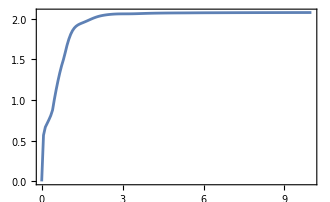

```mathematica
ListLinePlot@Table[{t,vonNeumann[ρt[t]]},{t,linspace[0,tf,150]}]
```

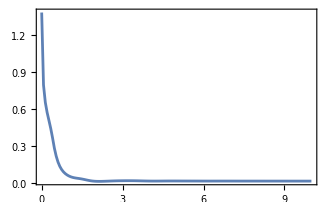

```mathematica
ListLinePlot[Table[{t,MutualInformation[ρt[t],{{1,2},{L}}]},{t,linspace[0,tf,150]}],PlotRange->All]
```

Concurrence between first and last sites

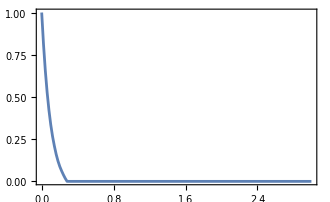

```mathematica
ListLinePlot@Table[
{t,Concurrence@PTr[ρt[t],{2,3}]},{t,linspace[0,3,150]}]
```

```mathematica
Concurrence@PTr[ρ0,{2,3}]
```

0